```mathematica
simpleMesh=<|"format"->"NTR","nodes"->{{0.,0.},{0.,1.},{1.,0.},{1.,1.}},"triangles"->{{1,0,2},{2,3,1}},"ribs"->{{0,1,2},{3,1,4}},"numb of ribs"->5|>;
```

```mathematica
plotShapes[ΔP1CR,simpleMesh,1]
```

-Graphics3D-

```mathematica
f[x_,y_]:=0;(*Sin[2 Pi x y]*)
```

```mathematica
ξ=computeDOFs[f,ΔP0L,𝒯];
```

```mathematica
Pξ=𝒫[ξ,ΔP0L,𝒯];
```

```mathematica
plot𝒫ξ[Pξ,𝒯]
```

-Graphics3D-

```mathematica
numbOf𝓃[𝒯]
```

53

```mathematica
p1=plotBasis[ΔP2L,𝒯,14,{Yellow,Opacity@.7}]
```

-Graphics3D-

```mathematica
p2=plotBasis[ΔP2L,𝒯,53+53,{Yellow,Opacity@.7}]
```

-Graphics3D-

```mathematica
Show[p2,p1]
```

-Graphics3D-

```mathematica
sizes={53,185,689,2657,10433,41345,164609,656897};
mgv={.025,.029,.035,.079,.222,.864,3.896,16.174};
mgw={.018,.034,.05,.111,.385,1.094,5.332,20.045};
pcg={.032,.024,.045,.077,.224,.826,2.858,12.907};
cg={.007,.031,.024,.14,.859,6.295,73.931,605.463};
```

```mathematica
mgv=Table[{sizes[[i]],mgv[[i]]},{i,8}];
mgw=Table[{sizes[[i]],mgw[[i]]},{i,8}];
pcg=Table[{sizes[[i]],pcg[[i]]},{i,8}];
cg=Table[{sizes[[i]],cg[[i]]},{i,8}];
```

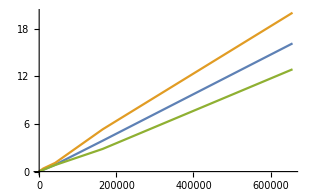
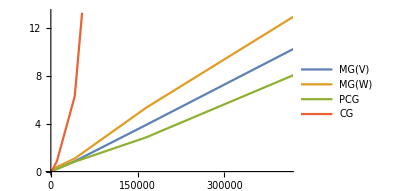

```mathematica
Row[{
ListLinePlot[{mgv,mgw,pcg},PlotRange->All,ImageSize->310],
ListLinePlot[{mgv,mgw,pcg,cg},PlotLegends->Placed[{"MG(V)","MG(W)","PCG","CG"},Left],ImageSize->310]
},"    "]
```